Más sobre las funciones puras

Se ha visto ya cómo formar listas y arreglos con Table. También las funciones puras pueden utilizarse para ese propósito, usando Array.

Genere un arreglo de 10 elementos mediante una función abstracta f:

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

Use una función pura para generar la lista de los 10 primeros cuadrados:

```mathematica
Array[#^2&,10]
```

{1,4,9,16,25,36,49,64,81,100}

Table permite obtener el mismo resultado, aunque en ese caso habría que introducir la variable n:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Array[f,4] forma una lista sencilla de 4 elementos. Array[f,{3,4}] forma un arreglo de 3×4.

Haga una lista de longitud 3, donde cada uno de sus elementos sea una lista de longitud 4:

```mathematica
Array[f,{3,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

Muestre lo anterior en una rejilla:

```mathematica
Array[f,{3,4}]//Grid
```

f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4]

En el caso de que la función fuera Times, Array construiría una tabla de multiplicar:

```mathematica
Grid[Array[Times,{5,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Y, ¿si se quiere usar una función pura en vez de Times? Cuando se calcula Times[3,4], se está indicando que Times se aplique a dos argumentos. (En Times[3,4,5], Times se aplica a tres argumentos, etc.). En una función pura, #1 representa al primer argumento, #2 al segundo argumento, y así sucesivamente.

#1 representa el primer argumento, #2 el segundo argumento:

```mathematica
f[#1,#2]&[55,66]
```

f[55,66]

#1 siempre elige el primer argumento, y #2 el segundo argumento:

```mathematica
f[#2,#1,{#2,#2,#1}]&[55,66]
```

f[66,55,{66,66,55}]

Ahora se podrá usar #1 y #2 dentro de una función en Array.

Use una función pura para formar una tabla de multiplicar:

```mathematica
Array[#1*#2&,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Use una función pura diferente que ponga una x siempre que los números sean iguales:

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Aquí se ve el cálculo equivalente efectuado mediante Table:

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Vistas las funciones puras con más de un argumento, se puede comenzar a ver FoldList. Puede considerarse a FoldList como una generalización de NestList cuando se tienen dos argumentos.

NestList toma una función individual, tal como f, y la va anidando sucesivamente:

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Esto puede comprenderse mejor si se usa la función Framed:

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

NestList simplemente aplica de nuevo una función al resultado obtenido en el último paso, cualquiera que sea. FoldList hace lo mismo salvo que, adicionalmente, incorpora un nuevo elemento cada vez.

Aquí se presenta FoldList con una función abstracta f:

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

Si se usa la función Framed se hace un poco más fácil comprender lo que sucede:

```mathematica
FoldList[Framed[f[#1,#2]]&,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

De entrada, esto puede parecer complicado y oscuro, y se hace difícil imaginar de qué manera podría ser útil. Sin embargo, efectivamente lo es, y es también insospechadamente común en programas reales.

FoldList es muy apropiado para acumular cosas progresivamente. Tómese de entrada un caso sencillo: sumar números progresivamente.

En cada paso FoldList incorpora otro elemento (#2), añadiéndolo al resultado que se ha obtenido hasta ese momento (#1):

```mathematica
FoldList[#1+#2&,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

Aquí se despliega el proceso que se va llevando a cabo:

```mathematica
{0,0+1,(0+1)+1,((0+1)+1)+1,(((0+1)+1)+1)+2,((((0+1)+1)+1)+2)+0,(((((0+1)+1)+1)+2)+0)+0}
```

{0,1,2,3,5,5,5}

O, de manera equivalente:

```mathematica
{0,0+1,0+1+1,0+1+1+1,0+1+1+1+2,0+1+1+1+2+0,0+1+1+1+2+0+0}
```

{0,1,2,3,5,5,5}

Puede ser más fácil ver lo que sucede si se usan símbolos:

```mathematica
FoldList[#1+#2&,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

Desde luego, este caso es demasiado sencillo y no se necesita recurrir a una función pura:

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

Un uso clásico de FoldList es en la incorporación sucesiva de dígitos para reconstruir un número a partir de la lista de sus dígitos.

Construya un número, de manera sucesiva, a partir de sus dígitos, comenzando el proceso de incorporación con el primer dígito:

```mathematica
FoldList[10#1+#2&,{8,7,6,1,2,3,9,8,7}]
```

{8,87,876,8761,87612,876123,8761239,87612398,876123987}

Por último, se usará FoldList para incorporar imágenes progresivas de una lista, añadiendo una, en cada paso, con ImageAdd a la imagen obtenida hasta ese momento.

Incorpore progresivamente imágenes de una lista, usando ImageAdd para combinarlas:

```mathematica
FoldList[ImageAdd,
{ -Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics- }]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Al principio, el concepto de FoldList no es lo más sencillo de comprender. Pero una vez que se adquiere familiaridad con él, se habrá aprendido una técnica por demás poderosa de la programación funcional, que ejemplifica el tipo de abstracción elegante que se hace posible con Wolfram Language.

Vocabulario

Array[f,n] |   | forma un arreglo mediante la aplicación de una función 
Array[f,{m,n}] |   | forma un arreglo de 2 dimensiones
FoldList[f,x,list] |   | aplica una función sucesivamente, incorporando los elementos de una lista

"6 Exercises Available"
"with 1 extras" | "Get Started »"

Use Prime y Array para generar la lista de los 100 primeros primos. »

| Expected output: |  
  | {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541} |

Use Prime y Array para encontrar las diferencias sucesivas entre los 100 primeros primos. »

| Expected output: |  
  | {1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18} |

Use Array y Grid para formar una tabla de sumar de 10 por 10. »

| Expected output: |  
  | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 |

Use FoldList, Times y Range para multiplicar los números hasta el 10 sucesivamente (formando los factoriales). »

| Expected output: |  
  | {1,1,2,6,24,120,720,5040,40320,362880,3628800} |

Use FoldList y Array para calcular los productos sucesivos de los 10 primeros primos. »

| Expected output: |  
  | {1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230} |

Use FoldList para aplicar ImageAdd sucesivamente a los polígonos regulares de 3 a 8 lados, con opacidad 0.2. »

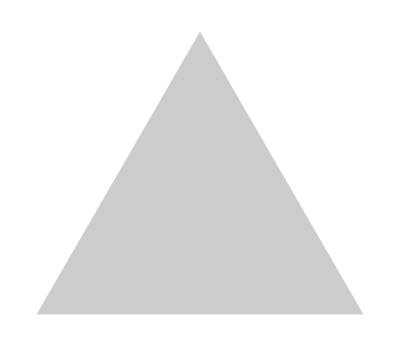
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use Array para formar una rejilla de 10 por 10, donde los elementos en la diagonal principal y abajo de ella sean 1, y el resto sean 0. »

| Expected output: |  
  | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |

Preguntas y respuestas

¿Qué significa # por sí solo?

Es equivalente a #1, una ranura que se llena con el primer argumento de una función.

¿Cómo se dice #1?

Ya sea como “slot 1” (que refleja su papel en una función pura), o “hash 1” (que refleja el cómo está escrito; la “#” se conoce usualmente como “hash”).

¿Se pueden denominar los argumentos de una función pura?

Sí. Eso se hace con Function[{x,y},x+y], etc. A veces está bien hacerlo así para mejorar la legibilidad del código, pero a veces es necesario cuando se anidan funciones puras.

¿Puede Array formar estructuras con anidación de mayor profundidad?

Sí, con tanta profundidad como se desee. Listas de listas de listas... hasta cualquier número de niveles.

¿Qué es la programación funcional?

Es un paradigma de programación basado en evaluación de funciones y en combinaciones de funciones. De hecho, es el único estilo de programación que se ha visto en el libro hasta el momento. En la Sección 38 se verá la programación por procedimientos, basada en moverse a través de algún procedimiento en el que se van cambiando progresivamente los valores de las variables.

Notas técnicas

Fold da el último elemento de FoldList, del mismo modo que Nest da el último elemento de NestList.

FromDigits reconstruye números a partir de la lista de sus dígitos y, de hecho, hace lo mismo que se hizo antes con FoldList.

Accumulate[lista] es lo mismo que FoldList[Plus,lista].

Array y FoldList, al igual que NestList, son ejemplos de lo que se llama funciones de orden superior, que toman funciones como entrada. (En matemáticas se conocen también como funcionales, o funtores).

Pueden armarse funciones puras que tomen cualquier número de argumentos a la vez, usando # #, etc.

Puede darse animación a listas de imágenes usando ListAnimate, y mostrarse las imágenes apiladas en 3D mediante Image3D.

Para explorar más

Guía para programación funcional en Wolfram Language »